## Data is from Plot1

## λ=0.01

```mathematica
results001t1={{1/10,0.057798234923685854,-0.0033678462988465663,151.4025270281629,0.05773502691896259-0.0032 ⅈ},{3/10,0.17659336698536054,-0.029693968261048975,71.89274124014207,0.17320508075688773-0.0288 ⅈ},{1/2,0.3027662001549646,-0.07730157869586396,36.9521312478857,0.2886751345948129-0.08 ⅈ}};
results001t2={{3/5,0.3813297838009094,-0.10866689767907434,44.639258959082504,0.34641016151377546-0.1152 ⅈ},{4/5,0.5377005562138762,-0.18540307581211124,53.233361978810684,0.4618802153517007-0.2048 ⅈ}};
results001t3={{9/10,0.6298798560157215,-0.23888137217553151,79.1153491406053,0.5196152422706631-0.2592 ⅈ},{1,0.7279589065781498,-0.27896320259105,235.80809267085627,0.5773502691896258-0.32 ⅈ}};
results001t4={{11/10,0.8325438397017222,-0.3236760069199245,145.64767038764023,0.6350852961085884-0.3872 ⅈ}};

results001=Join[results001t1,results001t2,results001t3,results001t4];
```

## λ=0.2

```mathematica
results021={{1/10,0.05817903060706234,-0.002563423343954513,6.531025706307207,0.05773502691896259-0.0006666666666666666 ⅈ},{1/10,0.05585313377470125,-0.0048153428350704575,3.506056104775642,0.05773502691896259-0.0006666666666666666 ⅈ},{3/10,0.17082101329992416,-0.006106742382492647,25.43016427734471,0.17320508075688773-0.006 ⅈ},{1/2,0.2840103553902007,-0.015111631131040637,26.85745442686312,0.2886751345948129-0.016666666666666666 ⅈ},{7/10,0.39315695668081196,-0.0381621646652015,39.97400728265226,0.40414518843273806-0.03266666666666666 ⅈ},{9/10,0.5063784373775813,-0.06812551647146092,25.28992110932445,0.5196152422706631-0.054 ⅈ},{11/10,0.6018816356520555,-0.10232361949774016,902.3580595783387,0.6350852961085884-0.08066666666666666 ⅈ},{13/10,0.6903644620317675,-0.14955640324340636,42.33112045976078,0.7505553499465136-0.11266666666666666 ⅈ}};
results022={{1/10,0.05771397618683463,-0.0006779819900132886,1161.9575925479176,0.05773502691896259-0.0006666666666666666 ⅈ},{1/5,0.11522069342299086,-0.0026807833114900516,646.8862864335986,0.11547005383792518-0.0026666666666666666 ⅈ},{3/10,0.17253125892138255,-0.006088673131629575,1063.5093537375383,0.17320508075688773-0.006 ⅈ},{2/5,0.22994285672846487,-0.011152390073915013,82.35092972657627,0.23094010767585035-0.010666666666666666 ⅈ},{1/2,0.2876927592865138,-0.01748571795371064,31.96798854396426,0.2886751345948129-0.016666666666666666 ⅈ}(*,{3/5,0.3454161303242206,-0.024948804045368155,19.30585471360777,0.34641016151377546-0.024 ⅈ},{7/10,0.4032077500954324,-0.03363522600216125,13.33258721701401,0.40414518843273806-0.03266666666666666 ⅈ}*)};
results02=Join[results021,results022];
```

```mathematica
Length[results02]
```

13

## λ=0.249

```mathematica
p1={{1/10,0.055680211675135705,-0.0005349411792558989,1.875649726414029,0.05773502691896259-0.000013333333333333333 ⅈ}};
p2={{3/10,0.17118602490797807,-0.0018241444941101692,3.1992642572292906,0.17320508075688773-0.00012 ⅈ},{1/2,0.2830055224423901,-0.0023025670265685028,3.1708634551018644,0.2886751345948129-0.0003333333333333333 ⅈ},{7/10,0.3975688558062519,-0.001672004816786754,5.380570711719438,0.40414518843273806-0.0006533333333333333 ⅈ}};
results249=Join[p1,p2];
```

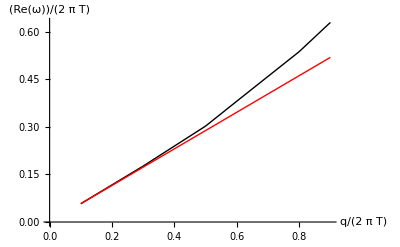

```mathematica
P001=ListPlot[{Table[{results001[[j,1]],results001[[j,2]]},{j,1,6}],Table[{results001[[j,1]],results001[[j,5]]//Re},{j,1,6}]},AxesOrigin->{0,0},AxesLabel->{q/(2 π T),Re[ω]/(2 π T)},PlotStyle->{Black,Red},Joined->True(*,Mesh->All*)]
```

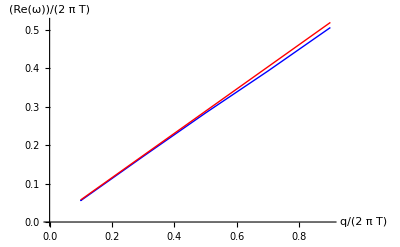

```mathematica
P02=ListPlot[{Table[{results02[[j,1]],results02[[j,2]]},{j,1,6}],Table[{results02[[j,1]],results02[[j,5]]//Re},{j,1,6}]},AxesOrigin->{0,0},AxesLabel->{q/(2 π T),Re[ω]/(2 π T)},PlotStyle->{Blue,Red},Joined->True(*,Mesh->All*)]
```

```mathematica
(*P0249=ListPlot[{Table[{results249[[j,1]],results249[[j,2]]},{j,1,4}],Table[{results249[[j,1]],results249[[j,5]]//Re},{j,1,4}]},AxesOrigin->{0.0,0},PlotStyle->{Red,Green},Joined->True]*)
```

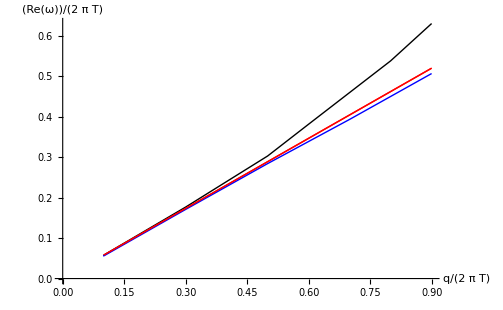

```mathematica
Show[P001,P02(*,P0249*)]
```

## Plot the imaginary part as well

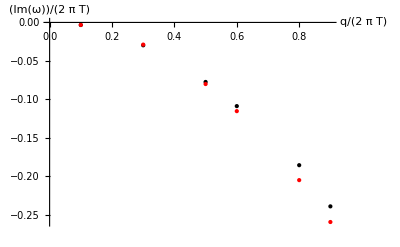

```mathematica
P001im=ListPlot[{Table[{results001[[j,1]],results001[[j,3]]},{j,1,6}],Table[{results001[[j,1]],results001[[j,5]]//Im},{j,1,6}]},AxesOrigin->{0,0},AxesLabel->{q/(2 π T),Im[ω]/(2 π T)},PlotStyle->{Black,Red}(*,Joined->True*)(*,Mesh->All*)]
```

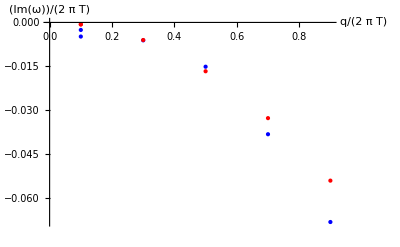

```mathematica
P02im=ListPlot[{Table[{results02[[j,1]],results02[[j,3]]},{j,1,6}],Table[{results02[[j,1]],results02[[j,5]]//Im},{j,1,6}]},AxesOrigin->{0,0},AxesLabel->{q/(2 π T),Im[ω]/(2 π T)},PlotStyle->{Blue,Red}(*,Joined->True*)(*,Mesh->All*)]
```

```mathematica
Show[P001im,P02im]
```

-Graphics-